# Simulate consumer-resource models with externally-supplied resources

```mathematica
ClearAll["Global`*"]
$HistoryLength = 0;
```

## Consumer-Resource models

### Shared model functions

```mathematica
GenerateGrowthConsumption[M_, S_, μg_, σg_, μc_, σc_, ρ_] := Module[{
		xC,
		xG,
		growth,
		consumption},
		
		xC = RandomVariate[NormalDistribution[0, 1], {M, S}]; 
		xG = RandomVariate[NormalDistribution[0, 1], {S, M}]; 
		
		growth = μg/M+σg/(√M)*xG;
		consumption = μc/M+σc/(√M)*(ρ*Transpose[xG] + √(1 - ρ^2)*xC);
		
		{growth, consumption}
	];
	
SimulateDynamicsCRM[dRNdt_, M_, S_, tEnd_] := Module[{

		SolveODE,
		
		initR,
	    initN,
	    initRPerturbed,
	    initNPerturbed,
	 
	    solution,
	    solutionPerturbed,
	    tLast,
	    tLastP,
	    evaluatedSolution,
	    evaluatedSolutionPerturbed,
	    distanceTrajectory,
	    maxLE,
	    output},
	    
	    SolveODE[initResource_, initConsumer_] := Module[{sol, status},
	    
	    sol = Quiet[TimeConstrained[NDSolve[Join[dRNdt[t],
													 {Resource[0] == initResource, Species[0] == initConsumer,
													 WhenEvent[Max[Abs[Resource[t]], Abs[Species[t]]] > 10^6, "StopIntegration"]}],
											   {Resource, Species},
											   {t, 0, tEnd},
											   Method -> {"StiffnessSwitching", "Method" ->{"ExplicitRungeKutta", Automatic}},
											   AccuracyGoal -> 9, PrecisionGoal -> 7],
									120, $Failed]];
	    
	    sol
	    
	    ];
	    
	    initR = RandomVariate[UniformDistribution[{10^-8, 2/M}], M];
		initN = RandomVariate[UniformDistribution[{10^-8, 2/S}], S];
						   
		solution = SolveODE[initR, initN];
						   
		If[solution === $Failed,
			(output = <|"ResourceDynamics" -> $Failed, "ConsumerDynamics" -> $Failed, "EndTime" -> $Failed, "maxLe" -> $Failed|>),
			(tLast = solution[[1, 1, 2]]["Domain"][[1, 2]];
			
			evaluatedSolution = <|"ResourceDynamics" -> Table[Evaluate[Resource[t]/.solution[[1]]], {t, Subdivide[0, tLast, 200]}],
							      "ConsumerDynamics" -> Table[Evaluate[Species[t]/.solution[[1]]], {t, Subdivide[0, tLast, 200]}]|> // Quiet;
							 
			initRPerturbed = initR + 10^-6;
			initNPerturbed = initN + 10^-6;
		
			solutionPerturbed = SolveODE[initRPerturbed, initNPerturbed];
			
			If[solutionPerturbed === $Failed,
				(output = Join[evaluatedSolution, <|"EndTime" -> tLast, "maxLe" -> $Failed|>]),
				(
				evaluatedSolutionPerturbed = {Table[Evaluate[Resource[t]/.solutionPerturbed[[1]]], {t, Subdivide[0, tLast, 200]}],
										  Table[Evaluate[Species[t]/.solutionPerturbed[[1]]], {t, Subdivide[0, tLast, 200]}]} // Quiet;
									  
				distanceTrajectory = Log[10, MapThread[EuclideanDistance, {Join[evaluatedSolution["ResourceDynamics"],
																			    evaluatedSolution["ConsumerDynamics"], 2],
																			Join[evaluatedSolutionPerturbed[[1]], evaluatedSolutionPerturbed[[2]], 2]}]];					
		
				maxLE = LinearModelFit[Transpose[{Subdivide[0, tLast, 200], distanceTrajectory}], {1, x}, x]["BestFitParameters"][[2]];
							 					 
				output = Join[evaluatedSolution, <|"EndTime" -> tLast, "maxLe" -> maxLE|>])]
	
		)];
	
	output
	
	];
	
SimulateDynamicsAbioticBioticCRM[dRNdt_, M_, S_, gammaR_, tEnd_] := Module[{

		SolveODE,
		
		initRA,
		initRB,
	    initN,
	    initRAPerturbed,
	    initRBPerturbed,
	    initNPerturbed,
	 
	    solution,
	    solutionPerturbed,
	    tLast,
	    tLastP,
	    evaluatedSolution,
	    evaluatedSolutionPerturbed,
	    distanceTrajectory,
	    maxLE,
	    output},
	    
	    SolveODE[initResourceA_, initResourceB_, initConsumer_] := Module[{sol, status},
	    
	    sol = Quiet[TimeConstrained[NDSolve[Join[dRNdt[t],
													 {abioticResource[0] == initResourceA, bioticResource[0] == initResourceB, Species[0] == initConsumer,
													 WhenEvent[Max[Abs[abioticResource[t]], Abs[bioticResource[t]], Abs[Species[t]]] > 10^6, "StopIntegration"]}],
											   {abiotcResource, bioticResource, Species},
											   {t, 0, tEnd},
											   Method -> {"StiffnessSwitching", "Method" ->{"ExplicitRungeKutta", Automatic}},
											   AccuracyGoal -> 9, PrecisionGoal -> 7],
									120, $Failed]];
	    
	    sol
	    
	    ];
	    
	    initRA = RandomVariate[UniformDistribution[{10^-8, 2/(M*gammaR)}], M*gammaR];
	    initRB = RandomVariate[UniformDistribution[{10^-8, 2/(M*(1-gammaR))}], M*(1-gammaR)];
		initN = RandomVariate[UniformDistribution[{10^-8, 2/S}], S];
						   
		solution = SolveODE[initRA, initRB, initN];
						   
		If[solution === $Failed,
			(output = <|"ResourceDynamics" -> $Failed, "ConsumerDynamics" -> $Failed, "EndTime" -> $Failed, "maxLe" -> $Failed|>),
			(tLast = solution[[1, 1, 2]]["Domain"][[1, 2]];
			
			evaluatedSolution = <|"AbioticResourceDynamics" -> Table[Evaluate[abioticResource[t]/.solution[[1]]], {t, Subdivide[0, tLast, 200]}],
								 "BioticResourceDynamics" -> Table[Evaluate[bioticResource[t]/.solution[[1]]], {t, Subdivide[0, tLast, 200]}],
							      "ConsumerDynamics" -> Table[Evaluate[Species[t]/.solution[[1]]], {t, Subdivide[0, tLast, 200]}]|> // Quiet;
							 
			initRAPerturbed = initRA + 10^-6;
			initRBPerturbed = initRB + 10^-6;
			initNPerturbed = initN + 10^-6;
		
			solutionPerturbed = SolveODE[initRPerturbed, initNPerturbed];
			
			If[solutionPerturbed === $Failed,
				(output = Join[evaluatedSolution, <|"EndTime" -> tLast, "maxLe" -> $Failed|>]),
				(
				evaluatedSolutionPerturbed = {Table[Evaluate[abioticResource[t]/.solutionPerturbed[[1]]], {t, Subdivide[0, tLast, 200]}],
											 Table[Evaluate[bioticResource[t]/.solutionPerturbed[[1]]], {t, Subdivide[0, tLast, 200]}],
										     Table[Evaluate[Species[t]/.solutionPerturbed[[1]]], {t, Subdivide[0, tLast, 200]}]} // Quiet;
									  
				distanceTrajectory = Log[10, MapThread[EuclideanDistance, {Join[evaluatedSolution["ResourceDynamics"],
																			    evaluatedSolution["ConsumerDynamics"], 2],
																			Join[evaluatedSolutionPerturbed[[1]], evaluatedSolutionPerturbed[[2]], 2]}]];					
		
				maxLE = LinearModelFit[Transpose[{Subdivide[0, tLast, 200], distanceTrajectory}], {1, x}, x]["BestFitParameters"][[2]];
							 					 
				output = Join[evaluatedSolution, <|"EndTime" -> tLast, "maxLe" -> maxLE|>])]
	
		)];
	
	output
	
	];
	
SimulateDynamicsELV[dRNdt_, S_, tEnd_] := Module[{

		SolveODE,
		
	    initN,
	    initNPerturbed,
	 
	    solution,
	    solutionPerturbed,
	    tLast,
	    tLastP,
	    evaluatedSolution,
	    evaluatedSolutionPerturbed,
	    distanceTrajectory,
	    maxLE,
	    output},
	    
	    SolveODE[initConsumer_] := Module[{sol, status},
	    
	    sol = Quiet[TimeConstrained[NDSolve[Join[dRNdt[t],
												{Species[0] == initConsumer,
												WhenEvent[Abs[Species[t]] > 10^6, "StopIntegration"]}],
											   {Species},
											   {t, 0, tEnd},
											   Method -> {"StiffnessSwitching", "Method" ->{"ExplicitRungeKutta", Automatic}},
											   AccuracyGoal -> 9, PrecisionGoal -> 7, MaxSteps -> 10000],
									120, $Failed]];
	    
	    sol
	    
	    ];
	    
		initN = RandomVariate[UniformDistribution[{10^-8, 2/S}], S];
						   
		solution = SolveODE[initN];
						   
		If[solution === $Failed,
			(output = <|"ConsumerDynamics" -> $Failed, "EndTime" -> $Failed, "maxLe" -> $Failed|>),
			(tLast = solution[[1, 1, 2]]["Domain"][[1, 2]];
			
			evaluatedSolution = <|"ConsumerDynamics" -> Table[Evaluate[Species[t]/.solution[[1]]], {t, Subdivide[0, tLast, 200]}]|> // Quiet;
							 
			initNPerturbed = initN + 10^-6;
		
			solutionPerturbed = SolveODE[initNPerturbed];
			
			If[solutionPerturbed === $Failed,
				(output = Join[evaluatedSolution, <|"EndTime" -> tLast, "maxLe" -> $Failed|>]),
				(
				evaluatedSolutionPerturbed = {Table[Evaluate[Species[t]/.solutionPerturbed[[1]]], {t, Subdivide[0, tLast, 200]}]} // Quiet;
									  
				distanceTrajectory = Log[10, MapThread[EuclideanDistance, {evaluatedSolution["ConsumerDynamics"],
																		  evaluatedSolutionPerturbed[[1]]}]];					
		
				maxLE = LinearModelFit[Transpose[{Subdivide[0, tLast, 200], distanceTrajectory}], {1, x}, x]["BestFitParameters"][[2]];
							 					 
				output = Join[evaluatedSolution, <|"EndTime" -> tLast, "maxLe" -> maxLE|>])]
	
		)];
	
	output
	
	];
	
CommunityProperties[abundances_] := Module[{
	
		phiA,
		Amean,
		Afluct},
		
		phiA = N[Count[abundances, x_ /; x > 10^-4]/Length[abundances]];
		Amean = Mean[abundances];
		Afluct = Mean[abundances^2];
		
		{phiA, Amean, Afluct}
		
	];
```

### Standard consumer-resource models

```mathematica
AbioticCRM[parameters_Association, simulation_Association] := Module[{
	
	M = parameters["M"],
	S = parameters["S"],
    ρ = parameters["ρ"],
    μc = parameters["μc"],
    σc = parameters["σc"],
    μg = parameters["μg"],
    σg = parameters["σg"],
    μd = parameters["μd"],
    σd = parameters["σd"],
    μb = parameters["μb"],
    σb = parameters["σb"],
    μo = parameters["μo"],
    σo = parameters["σo"],
    
    tEnd = simulation["tEnd"],
    
    growth,
    consumption,
    death,
    influx,
    outflux,
    dRNdtAbiotic,
    
    simulatedDynamics,
    resourceProperties,
    consumerProperties,
    
    output

	},
	
	dRNdtAbiotic[t_] := Module[{},

	{Resource'[t] == influx - outflux*Resource[t] - Resource[t]*(consumption.Species[t]) + 10^-8,
	 Species'[t] == Species[t]*(growth.Resource[t] - death) + 10^-8}

	];
	
	{growth, consumption} = GenerateGrowthConsumption[M, S, μg, σg, μc, σc, ρ];
	death = μd + σd*RandomVariate[NormalDistribution[], S];
	influx = μb + σb*RandomVariate[NormalDistribution[], M];
	outflux = μo + σo*RandomVariate[NormalDistribution[], M];
	
	simulatedDynamics = SimulateDynamicsCRM[dRNdtAbiotic, M, S, tEnd];
	
	If[simulatedDynamics["ResourceDynamics"] === $Failed,
		(output = Join[simulatedDynamics, AssociationMap[$Failed &, {"phiR", "Rmean", "Rfluct", "phiN", "Nmean", "Nfluct"}]];),
		(resourceProperties = CommunityProperties[simulatedDynamics["ResourceDynamics"][[-1]]];
		consumerProperties = CommunityProperties[simulatedDynamics["ConsumerDynamics"][[-1]]];
	
		output = Join[simulatedDynamics, AssociationThread[{"phiR", "Rmean", "Rfluct", "phiN", "Nmean", "Nfluct"},
														   Join[resourceProperties, consumerProperties]]])
	];
	
	output
	
];

BioticCRM[parameters_Association, simulation_Association] := Module[{
	
	M = parameters["M"],
	S = parameters["S"],
    ρ = parameters["ρ"],
    μc = parameters["μc"],
    σc = parameters["σc"],
    μg = parameters["μg"],
    σg = parameters["σg"],
    μd = parameters["μd"],
    σd = parameters["σd"],
    μb = parameters["μb"],
    σb = parameters["σb"],
    
    tEnd = simulation["tEnd"],
    
    growth,
    consumption,
    death,
    influx,
    
    dRNdtBiotic,
    
    simulatedDynamics,
    resourceProperties,
    consumerProperties,
    
    output

	},
	
	dRNdtBiotic[t_] := Module[{},

	{Resource'[t] == Resource[t]*(influx - Resource[t] -  consumption.Species[t]) + 10^-8,
	 Species'[t] == Species[t]*(growth.Resource[t] - death) + 10^-8}

	];
	
	{growth, consumption} = GenerateGrowthConsumption[M, S, μg, σg, μc, σc, ρ];
	death = μd + σd*RandomVariate[NormalDistribution[], S];
	influx = μb + σb*RandomVariate[NormalDistribution[], M];
	
	simulatedDynamics = SimulateDynamicsCRM[dRNdtBiotic, M, S, tEnd];
	
	If[simulatedDynamics["ResourceDynamics"] === $Failed,
		(output = Join[simulatedDynamics, AssociationMap[$Failed &, {"phiR", "Rmean", "Rfluct", "phiN", "Nmean", "Nfluct"}]];),
		(resourceProperties = CommunityProperties[simulatedDynamics["ResourceDynamics"][[-1]]];
		consumerProperties = CommunityProperties[simulatedDynamics["ConsumerDynamics"][[-1]]];
	
		output = Join[simulatedDynamics, AssociationThread[{"phiR", "Rmean", "Rfluct", "phiN", "Nmean", "Nfluct"},
														   Join[resourceProperties, consumerProperties]]])
	];
	
	output
	
];
```

### Mixed resource supply models

```mathematica
HybridResourceCRM[parameters_Association, simulation_Association] := Module[{
	
	M = parameters["M"],
	S = parameters["S"],
    ρ = parameters["ρ"],
    μc = parameters["μc"],
    σc = parameters["σc"],
    μg = parameters["μg"],
    σg = parameters["σg"],
    μd = parameters["μd"],
    σd = parameters["σd"],
    μb = parameters["μb"],
    σb = parameters["σb"],
    μo = parameters["μo"],
    σo = parameters["σo"],
    μsi = parameters["μsi"],
    σsi = parameters["σsi"],
    
    tEnd = simulation["tEnd"],
    
    growth,
    consumption,
    death,
    influx,
    outflux,
    selfInhibition,
    dRNdtAbiotic,
    
    simulatedDynamics,
    resourceProperties,
    consumerProperties,
    
    output

	},
	
	dRNdtAbiotic[t_] := Module[{},

	{Resource'[t] == influx + Resource[t]*(outflux - selfInhibition*Resource[t]) - Resource[t]*(consumption.Species[t]) + 10^-8,
	 Species'[t] == Species[t]*(growth.Resource[t] - death) + 10^-8}

	];
	
	{growth, consumption} = GenerateGrowthConsumption[M, S, μg, σg, μc, σc, ρ];
	death = μd + σd*RandomVariate[NormalDistribution[], S];
	influx = μb + σb*RandomVariate[NormalDistribution[], M];
	outflux = μo + σo*RandomVariate[NormalDistribution[], M];
	selfInhibition = μsi + σsi*RandomVariate[NormalDistribution[], M];
	
	simulatedDynamics = SimulateDynamicsCRM[dRNdtAbiotic, M, S, tEnd];
	
	If[simulatedDynamics["ResourceDynamics"] === $Failed,
		(output = Join[simulatedDynamics, AssociationMap[$Failed &, {"phiR", "Rmean", "Rfluct", "phiN", "Nmean", "Nfluct"}]];),
		(resourceProperties = CommunityProperties[simulatedDynamics["ResourceDynamics"][[-1]]];
		consumerProperties = CommunityProperties[simulatedDynamics["ConsumerDynamics"][[-1]]];
	
		output = Join[simulatedDynamics, AssociationThread[{"phiR", "Rmean", "Rfluct", "phiN", "Nmean", "Nfluct"},
														   Join[resourceProperties, consumerProperties]]])
	];
	
	output
	
];

AbioticandBioticCRM[parameters_Association, simulation_Association] := Module[{
	
	M = parameters["M"],
	gammaR = parameters["M"];
	S = parameters["S"],
    ρ = parameters["ρ"],
    μc = parameters["μc"],
    σc = parameters["σc"],
    μg = parameters["μg"],
    σg = parameters["σg"],
    μd = parameters["μd"],
    σd = parameters["σd"],
    μb = parameters["μb"],
    σb = parameters["σb"],
    μo = parameters["μo"],
    σo = parameters["σo"],
    
    tEnd = simulation["tEnd"],
    
    growth,
    consumption,
    death,
    influxA,
    influxB,
    outflux,
    dRNdtAbiotic,
    
    simulatedDynamics,
    resourceProperties,
    consumerProperties,
    
    output

	},
	
	dRNdtAbiotic[t_] := Module[{},

	{abioticResource'[t] == influxA - outflux*abioticResource[t] - abioticResource[t]*(consumption.Species[t]) + 10^-8,
	 bioticResource'[t] == bioticResource[t]*(influxB - bioticResource[t] -  consumption.Species[t]) + 10^-8,
	 Species'[t] == Species[t]*(growth.Join[abioticResource[t], bioticResource[t]] - death) + 10^-8}

	];
	
	{growth, consumption} = GenerateGrowthConsumption[M, S, μg, σg, μc, σc, ρ];
	death = μd + σd*RandomVariate[NormalDistribution[], S];
	
	influxA = μb + σb*RandomVariate[NormalDistribution[], M*gammaR];
	influxB = μb + σb*RandomVariate[NormalDistribution[], M*(1-gammaR)];
	
	outflux = μo + σo*RandomVariate[NormalDistribution[], M];
	
	simulatedDynamics = SimulateDynamicsCRM[dRNdtAbiotic, M, S, tEnd];
	
	If[simulatedDynamics["ResourceDynamics"] === $Failed,
		(output = Join[simulatedDynamics, AssociationMap[$Failed &, {"phiR", "Rmean", "Rfluct", "phiN", "Nmean", "Nfluct"}]];),
		(resourceProperties = CommunityProperties[simulatedDynamics["ResourceDynamics"][[-1]]];
		consumerProperties = CommunityProperties[simulatedDynamics["ConsumerDynamics"][[-1]]];
	
		output = Join[simulatedDynamics, AssociationThread[{"phiR", "Rmean", "Rfluct", "phiN", "Nmean", "Nfluct"},
														   Join[resourceProperties, consumerProperties]]])
	];
	
	output
	
];
```

### Effective Lotka-Volterra models

```mathematica
AbioticELV[parameters_Association, simulation_Association] := Module[{
	
	M = parameters["M"],
	S = parameters["S"],
    ρ = parameters["ρ"],
    μc = parameters["μc"],
    σc = parameters["σc"],
    μg = parameters["μg"],
    σg = parameters["σg"],
    μd = parameters["μd"],
    σd = parameters["σd"],
    μb = parameters["μb"],
    σb = parameters["σb"],
    μo = parameters["μo"],
    σo = parameters["σo"],
    
    tEnd = simulation["tEnd"],
    
    growth,
    consumption,
    death,
    influx,
    outflux,
    consumerGrowth, 
    interactionMatrix,
    
    dNdtAbiotic,
    
    simulatedDynamics,
    resourceProperties,
    consumerProperties,
    
    output

	},
	
	dNdtAbiotic[t_] := Module[{},

	{Species'[t] == Species[t]*(consumerGrowth - interactionMatrix.Species[t]) + 10^-8}

	];
	
	{growth, consumption} = GenerateGrowthConsumption[M, S, μg, σg, μc, σc, ρ];
	death = μd + σd*RandomVariate[NormalDistribution[], S];
	influx = μb + σb*RandomVariate[NormalDistribution[], M];
	outflux = μo + σo*RandomVariate[NormalDistribution[], M];
	
	consumerGrowth = growth.(influx/outflux) - death;
	
	interactionMatrix = Dot[growth * Threaded[influx/outflux^2], consumption];
	
	simulatedDynamics = SimulateDynamicsELV[dNdtAbiotic, S, tEnd];
	
	If[simulatedDynamics["ConsumerDynamics"] === $Failed,
		(output = Join[simulatedDynamics, AssociationMap[$Failed &, {"phiN", "Nmean", "Nfluct"}]];),
		(consumerProperties = CommunityProperties[simulatedDynamics["ConsumerDynamics"][[-1]]];
	
		output = Join[simulatedDynamics, AssociationThread[{"phiN", "Nmean", "Nfluct"},
														   consumerProperties]])
	];
	
	output
	
];

BioticELV[parameters_Association, simulation_Association] := Module[{
	
	M = parameters["M"],
	S = parameters["S"],
    ρ = parameters["ρ"],
    μc = parameters["μc"],
    σc = parameters["σc"],
    μg = parameters["μg"],
    σg = parameters["σg"],
    μd = parameters["μd"],
    σd = parameters["σd"],
    μb = parameters["μb"],
    σb = parameters["σb"],
    
    tEnd = simulation["tEnd"],
    
    growth,
    consumption,
    death,
    influx,
    consumerGrowth, 
    interactionMatrix,
    
    dNdtBiotic,
    
    simulatedDynamics,
    resourceProperties,
    consumerProperties,
    
    output

	},
	
	dNdtBiotic[t_] := Module[{},

	{Species'[t] == Species[t]*(consumerGrowth - interactionMatrix.Species[t]) + 10^-8}

	];
	
	{growth, consumption} = GenerateGrowthConsumption[M, S, μg, σg, μc, σc, ρ];
	death = μd + σd*RandomVariate[NormalDistribution[], S];
	influx = μb + σb*RandomVariate[NormalDistribution[], M];
	
	consumerGrowth = growth.influx - death;
	
	interactionMatrix = Dot[growth, consumption];
	
	simulatedDynamics = SimulateDynamicsELV[dNdtBiotic, S, tEnd];
	
	If[simulatedDynamics["ConsumerDynamics"] === $Failed,
		(output = Join[simulatedDynamics, AssociationMap[$Failed &, {"phiN", "Nmean", "Nfluct"}]];),
		(consumerProperties = CommunityProperties[simulatedDynamics["ConsumerDynamics"][[-1]]];
	
		output = Join[simulatedDynamics, AssociationThread[{"phiN", "Nmean", "Nfluct"},
														   consumerProperties]])
	];
	
	output
	
];
```

## Functions for running simulations across parameter space

```mathematica
StabilitySimulation[filename_, model_, parameterSets_Association, simulation_Association, nRep_: 20] := Module[{

    tEnd = simulation["tEnd"],
    
    FormatParams,
    
    varyingParams,
    fixedParams,
    paramNames,
    paramRanges,
    allCombinations,
    maxLEs,
    dataTemp,
    oldKeys,
    newKeys,
    output},
    
    FormatParams[params_Association] := Join[KeyDrop[params, {"μinteract", "σinteract"}], 
										         <|"μc" -> params["μinteract"], "σc" -> params["σinteract"], "μg" -> params["μinteract"], "σg" -> params["σinteract"]|>];
	
	varyingParams = Select[parameterSets, Length[#] > 0 &];
    fixedParams = Select[parameterSets, Length[#] === 0 &];
    
    paramNames = Keys[varyingParams];
    paramRanges = Values[varyingParams];
    allCombinations = Tuples[paramRanges];
    
    LaunchKernels[];
	DistributeDefinitions[StabilityParmSet, AbioticCRM, BioticCRM, HybridCRM, AbioticandBioticCRM, AbioticELV, BioticELV, SimulateDynamicsCRM, SimulateDynamicsELV, GenerateGrowthConsumption, CommunityProperties,
						 FormatParams];
    ParallelEvaluate[Off[Set::shape]];
    
    maxLEs = ParallelTable[Module[{paramSet},
								  paramSet = FormatParams[Join[fixedParams, AssociationThread[paramNames, parmcombo]]];
								  StabilityParmSet[model, paramSet, tEnd, nRep]],
						   {parmcombo, allCombinations}] // Quiet;
						   
	ParallelEvaluate[On[Set::shape]];
	
	dataTemp = Dataset[Flatten[maxLEs, 1]];
	oldKeys = Keys[Normal[dataTemp][[1]]];
	newKeys = oldKeys /. {"ρ" -> "rho", "μc" -> "mu_c", "σc" -> "sigma_c", 
	                      "μg" -> "mu_g", "σg" -> "sigma_g", "μd" -> "mu_d", 
	                      "σd" -> "sigma_d", "μb" -> "mu_b", "σb" -> "sigma_b",
	                      "μo" -> "mu_o", "σo" -> "sigma_o"};
	output = Dataset[Map[AssociationThread[newKeys, Values[#]] &, Normal[dataTemp]]];
	
	Export[filename, output, "CSV"];
];

StabilityParmSet[model_, paramSet_Association, tEnd_, nRep_] := Module[{
    
		Model,
		maxLeParmSet},
		
		Model = Switch[model, "AbioticCRM", AbioticCRM, "BioticCRM",  BioticCRM,
		                      "HybridCRM", HybridCRM, "AbioticandBioticCRM", AbioticandBioticCRM,
							 "AbioticELV", AbioticELV, "BioticELV",  BioticELV];
		
		maxLeParmSet = Table[Join[paramSet, KeyDrop[Model[paramSet, <|"tEnd" -> tEnd|>],
					                                {"ResourceDynamics", "ConsumerDynamics", "AbioticResourceDynamics", "BioticResourceDynamics"}]],
						{n, 1, nRep}] // Quiet;
			                 
		maxLeParmSet
											
	];
```

```mathematica
ExampleSimulationsCRM[model_, parameters_Association, directory_] := Module[{CRM, simulation, rDynamics, cDynamics, timeSteps, df, colNames, namedDf},

	CRM = Switch[model, "Abiotic", AbioticCRM, "Biotic",  BioticCRM];
	simulation = CRM[parameters, <|"tEnd" -> 400|>];
	
	rDynamics = Table[simulation["ResourceDynamics"][[All, alpha]], {alpha, 1, Length[simulation["ResourceDynamics"][[1, All]]]}];
	cDynamics = Table[simulation["ConsumerDynamics"][[All, alpha]], {alpha, 1, Length[simulation["ConsumerDynamics"][[1, All]]]}];
	
	timeSteps = Subdivide[0, simulation["EndTime"], 200];
	
	df = Append[Join[rDynamics, cDynamics, 1], timeSteps];
	
	colNames = Table[Join[Table["resource" <> ToString[i], {i, 1, Dimensions[rDynamics][[1]]}],
					 Table["consumer" <> ToString[i], {i, 1, Dimensions[cDynamics][[1]]}],
					 {"t"}]];
					 
	colNames = ToString /@ colNames;				 	 
					 
	namedDf = Prepend[Transpose[df], colNames];
	Export[directory, namedDf, "CSV"];

];

ExampleSimulationsELV[model_, parameters_Association, directory_] := Module[{ELV, simulation, cDynamics, timeSteps, df, colNames, namedDf},

	ELV = Switch[model, "Abiotic", AbioticELV, "Biotic",  BioticELV];
	simulation = CRM[parameters, <|"tEnd" -> 400|>];
	
	cDynamics = Table[simulation["ConsumerDynamics"][[All, alpha]], {alpha, 1, Length[simulation["ConsumerDynamics"][[1, All]]]}];
	
	timeSteps = Subdivide[0, simulation["EndTime"], 200];
	
	df = Append[cDynamics, timeSteps];
	
	colNames = Table[Join[Table["consumer" <> ToString[i], {i, 1, Dimensions[cDynamics][[1]]}],
					      {"t"}]];
					 
	colNames = ToString /@ colNames;				 	 
					 
	namedDf = Prepend[Transpose[df], colNames];
	Export[directory, namedDf, "CSV"];

];
```

## Consumer-resource model simulations

### Numerically-stable simulations

Parameter space where simulations are numerically-stable (chaotic dynamics emerge in the unstable feasible region of the BioticCRM), but the self-consistency equations are poorly solved.
(The saving protocol for the biotic model is slightly different/more regular than the abiotic model because Mathematica often crashes in the chaotic region.)

```mathematica
Do[StabilitySimulation["C:/Users/jamil/Documents/PhD/Data/external_resource_stability/simulations/rho_vs_sigma_biotic/rho_" <> ToString[ρval] <> ".csv",
						"BioticCRM",
						<|"M" -> 150, "S" -> 150,
					      "ρ" -> ρval, "μinteract" -> 50.0, "σinteract" -> Range[2.0, 12.0, 0.5],
					      "μd" -> 1.0, "σd" -> 0.1,
					      "μb" -> 1.0, "σb" -> 0.1|>,
					      <|"tEnd" -> 400|>, 30], 
					      {ρval, Range[0.1, 1.0, 0.1]}] // Quiet;

StabilitySimulation["C:/Users/jamil/Documents/PhD/Data/external_resource_stability/simulations/rho_vs_sigma_abiotic.csv",
					"AbioticCRM",
					<|"M" -> 150, "S" -> 150,
					  "ρ" -> Range[0.1, 1.0, 0.1], "μinteract" -> 50.0, "σinteract" -> Range[2.0, 12.0, 0.5],
					  "μd" -> 1.0, "σd" -> 0.1,
					  "μb" -> 1.0, "σb" -> 0.1,
					  "μo" -> 1.0, "σo" -> 0.0|>,
					  <|"tEnd" -> 400|>, 30] // Quiet;
```

Example dynamics for the stable and unstable feasible regions of each model.

```mathematica
ExampleSimulationsCRM["Abiotic", 
					<|"M" -> 150, "S" -> 150, "ρ" -> 0.4, "μc" -> 50.0, "σc" -> 10.5, "μg" -> 50.0, "σg" -> 10.5,
					  "μd" -> 1.0, "σd" -> 0.1, "μb" -> 1.0, "σb" -> 0.1, "μo" -> 1.0, "σo" -> 0.0|>,
					"C:/Users/jamil/Documents/PhD/Data/external_resource_stability/simulations/rho_vs_sigma_abiotic_unstable2.csv"]
					
ExampleSimulationsCRM["Biotic", 
					<|"M" -> 150, "S" -> 150, "ρ" -> 0.8, "μc" -> 50.0, "σc" -> 10.5, "μg" -> 50.0, "σg" -> 10.5,
					  "μd" -> 1.0, "σd" -> 0.1, "μb" -> 1.0, "σb" -> 0.1|>,
					"C:/Users/jamil/Documents/PhD/Data/external_resource_stability/simulations/rho_vs_sigma_biotic_unstable2.csv"]
					
ExampleSimulationsCRM["Abiotic", 
					<|"M" -> 150, "S" -> 150, "ρ" -> 1.0, "μc" -> 50.0, "σc" -> 10.5, "μg" -> 50.0, "σg" -> 10.5,
					  "μd" -> 1.0, "σd" -> 0.1, "μb" -> 1.0, "σb" -> 0.1, "μo" -> 1.0, "σo" -> 0.0|>,
					"C:/Users/jamil/Documents/PhD/Data/external_resource_stability/simulations/rho_vs_sigma_abiotic_stable2.csv"]
					
ExampleSimulationsCRM["Biotic", 
					<|"M" -> 150, "S" -> 150, "ρ" -> 1.0, "μc" -> 50.0, "σc" -> 10.5, "μg" -> 50.0, "σg" -> 10.5,
					  "μd" -> 1.0, "σd" -> 0.1, "μb" -> 1.0, "σb" -> 0.1|>,
					"C:/Users/jamil/Documents/PhD/Data/external_resource_stability/simulations/rho_vs_sigma_biotic_stable2.csv"]
```

### Numerically-unstable simulations

Parameter space where simulations are not numerically-stable (only unbounded dynamics are observed in the unstable feasible region of the BioticCRM), but the self-consistency equations are solved well.

```mathematica
StabilitySimulation["C:/Users/jamil/Documents/PhD/Data/external_resource_stability/simulations/rho_vs_sigma_biotic_smallmu.csv",
					"BioticCRM",
					<|"M" -> 150, "S" -> 150,
					  "ρ" -> Range[0.1, 1.0, 0.1], "μinteract" -> 1.0, "σinteract" -> Range[0.05, 2.0, 0.05],
					  "μd" -> 1.0, "σd" -> 0.1,
					  "μb" -> 1.0, "σb" -> 0.1|>,
					  <|"tEnd" -> 200|>, 30] // Quiet;

StabilitySimulation["C:/Users/jamil/Documents/PhD/Data/external_resource_stability/simulations/rho_vs_sigma_abiotic_smallmu.csv",
					"AbioticCRM",
					<|"M" -> 150, "S" -> 150,
					  "ρ" -> Range[0.1, 1.0, 0.1], "μinteract" -> 1.0, "σinteract" -> Range[0.05, 2.0, 0.05],
					  "μd" -> 1.0, "σd" -> 0.1,
					  "μb" -> 1.0, "σb" -> 0.1,
					  "μo" -> 1.0, "σo" -> 0.0|>,
					  <|"tEnd" -> 200|>, 30] // Quiet;
```

## Mixed model simulations

```mathematica
Do[StabilitySimulation["C:/Users/jamil/Documents/PhD/Data/external_resource_stability/simulations/unstable_dynamics_hybridmodel/b_" <> ToString[μbval] <> ".csv",
						"HybridRM",
						<|"M" -> 150, "S" -> 150,
					      "ρ" -> 0.3, "μinteract" -> 50.0, "σinteract" -> 10.5,
					      "μd" -> 1.0, "σd" -> 0.1,
					      "μb" -> μbval, "σb" -> 0.1
					      "μo" -> Range[-1.0, 1.0, 0.2], "σo" -> 0.1|>,
					      <|"tEnd" -> 400|>, 30], 
					      {μbval, Range[0.0, 1.0, 0.2]}] // Quiet;
```

```mathematica
Do[StabilitySimulation["C:/Users/jamil/Documents/PhD/Data/external_resource_stability/simulations/rho_vs_sigma_biotic/rho_" <> ToString[ρval] <> ".csv",
						"BioticCRM",
						<|"M" -> 150, "S" -> 150,
					      "ρ" -> ρval, "μinteract" -> 50.0, "σinteract" -> Range[2.0, 12.0, 0.5],
					      "μd" -> 1.0, "σd" -> 0.1,
					      "μb" -> 1.0, "σb" -> 0.1|>,
					      <|"tEnd" -> 400|>, 30], 
					      {ρval, Range[0.1, 1.0, 0.1]}] // Quiet;
```

## Effective Lotka-Volterra model simulations

```mathematica
Do[StabilitySimulation["C:/Users/jamil/Documents/PhD/Data/external_resource_stability/simulations/rho_vs_sigma_biotic_elv/rho_" <> ToString[ρval] <> ".csv",
						"BioticELV",
						<|"M" -> 150, "S" -> 150,
					      "ρ" -> ρval, "μinteract" -> 50.0, "σinteract" -> Range[2.0, 12.0, 0.5],
					      "μd" -> 1.0, "σd" -> 0.1,
					      "μb" -> 1.0, "σb" -> 0.0|>,
					      <|"tEnd" -> 400|>, 30], 
					      {ρval, Range[0.1, 1.0, 0.1]}] // Quiet;
					      
Do[StabilitySimulation["C:/Users/jamil/Documents/PhD/Data/external_resource_stability/simulations/rho_vs_sigma_abiotic_elv/rho_" <> ToString[ρval] <> ".csv",
						"AbioticELV",
						<|"M" -> 150, "S" -> 150,
					      "ρ" -> ρval, "μinteract" -> 50.0, "σinteract" -> Range[2.0, 12.0, 0.5],
					      "μd" -> 1.0, "σd" -> 0.1,
					      "μb" -> 1.0, "σb" -> 0.0,
					      "μo" -> 1.0, "σo" -> 0.0|>,
					      <|"tEnd" -> 400|>, 30], 
					      {ρval, Range[0.1, 1.0, 0.1]}] // Quiet;
```

```mathematica
ExampleSimulationsELV["Abiotic", 
					<|"M" -> 150, "S" -> 150, "ρ" -> 0.3, "μc" -> 50.0, "σc" -> 5.0, "μg" -> 50.0, "σg" -> 5.0,
					  "μd" -> 1.0, "σd" -> 0.1, "μb" -> 1.0, "σb" -> 0.0, "μo" -> 1.0, "σo" -> 0.0|>,
					"C:/Users/jamil/Documents/PhD/Data/external_resource_stability/simulations/rho_vs_sigma_abiotic_elv_unstable.csv"]
					
ExampleSimulationsELV["Biotic", 
					<|"M" -> 150, "S" -> 150, "ρ" -> 0.3, "μc" -> 50.0, "σc" -> 5.0, "μg" -> 50.0, "σg" -> 5.0,
					  "μd" -> 1.0, "σd" -> 0.1, "μb" -> 1.0, "σb" -> 0.0|>,
					"C:/Users/jamil/Documents/PhD/Data/external_resource_stability/simulations/rho_vs_sigma_biotic_elv_unstable.csv"]
					
ExampleSimulationsELV["Abiotic", 
					<|"M" -> 150, "S" -> 150, "ρ" -> 1.0, "μc" -> 50.0, "σc" -> 5.0, "μg" -> 50.0, "σg" -> 5.0,
					  "μd" -> 1.0, "σd" -> 0.1, "μb" -> 1.0, "σb" -> 0.0, "μo" -> 1.0, "σo" -> 0.0|>,
					"C:/Users/jamil/Documents/PhD/Data/external_resource_stability/simulations/rho_vs_sigma_abiotic_elv_stable.csv"]
					
ExampleSimulationsELV["Biotic", 
					<|"M" -> 150, "S" -> 150, "ρ" -> 1.0, "μc" -> 50.0, "σc" -> 5.0, "μg" -> 50.0, "σg" -> 5.0,
					  "μd" -> 1.0, "σd" -> 0.1, "μb" -> 1.0, "σb" -> 0.0|>,
					"C:/Users/jamil/Documents/PhD/Data/external_resource_stability/simulations/rho_vs_sigma_biotic_elv_stable.csv"]
```

## Testing ground

### Finding suitable parameter regions

```mathematica
ρtest = 0.3;
μtest = 50.0;
σtest = 10.5;

paramTestA = <|"M" -> 150, "S" -> 150, "ρ" -> ρtest, "μc" -> μtest, "σc" -> σtest, "μg" -> μtest, "σg" -> σtest,
			  "μd" -> 1.0, "σd" -> 0.1, "μb" -> 1.0, "σb" -> 0.1, "μo" -> 1.0, "σo" -> 0.0|>;
			  
paramTestB = <|"M" -> 150, "S" -> 150, "ρ" -> ρtest, "μc" -> μtest, "σc" -> σtest, "μg" -> μtest, "σg" -> σtest,
			  "μd" -> 1.0, "σd" -> 0.1, "μb" -> 1.0, "σb" -> 0.1|>;

simulationTestA = AbioticCRM[paramTestA, <|"tEnd" -> 700|>];
simulationTestB = BioticCRM[paramTestB, <|"tEnd" -> 700|>];
```

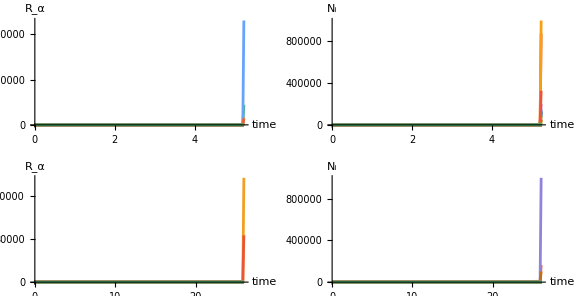

```mathematica
RdynamicsA = Table[simulationTestA["ResourceDynamics"][[ All, alpha]], {alpha, 1, Length[simulationTestA["ResourceDynamics"][[1, All]]]}];
NdynamicsA = Table[simulationTestA["ConsumerDynamics"][[All, alpha]], {alpha, 1, Length[simulationTestA["ConsumerDynamics"][[1, All]]]}];
RdynamicsB = Table[simulationTestB["ResourceDynamics"][[ All, alpha]], {alpha, 1, Length[simulationTestB["ResourceDynamics"][[1, All]]]}];
NdynamicsB = Table[simulationTestB["ConsumerDynamics"][[All, alpha]], {alpha, 1, Length[simulationTestB["ConsumerDynamics"][[1, All]]]}];

Show[GraphicsGrid[{{ListLinePlot[RdynamicsA, AxesLabel->{"time", "R_α"}, DataRange->{0, simulationTestA["EndTime"]}, AspectRatio->0.5, PlotRange -> All], 
				  ListLinePlot[NdynamicsA, AxesLabel->{"time", "N_i"}, DataRange->{0, simulationTestA["EndTime"]}, AspectRatio->0.5, PlotRange -> All]},
				  {ListLinePlot[RdynamicsB, AxesLabel->{"time", "R_α"}, DataRange->{0, simulationTestB["EndTime"]}, AspectRatio->0.5, PlotRange -> All], 
				  ListLinePlot[NdynamicsB, AxesLabel->{"time", "N_i"}, DataRange->{0, simulationTestB["EndTime"]}, AspectRatio->0.5, PlotRange -> All]}}], 
	ImageSize->Large]
```

### Setting suitable extinction thresholds (for calculating the consumer survival fraction)

```mathematica
Print[N[Count[simulationTestA["ConsumerDynamics"][[-1]], x_ /; x > 10^-6.5]/Length[simulationTestA["ConsumerDynamics"][[-1]]]], " ", simulationTestA[["Nmean"]], " ", simulationTestA[["Nfluct"]], " ", simulationTestA[["Rmean"]], " ", simulationTestA[["Rfluct"]]]
```

0.0466667 1.45962 101.764 0.0153166 0.000356902

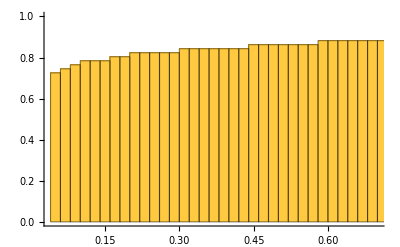

```mathematica
A = Table[N[Count[simulationTestA["ConsumerDynamics"][[-1]], x_ /; x > 10^extThresh]/Length[simulationTestA["ConsumerDynamics"][[-1]]]], {extThresh, Range[-3, -8, -0.1]}];

Show[Histogram[A, 50, "CDF"]]
```

### Testing the effective Lotka-Volterra model

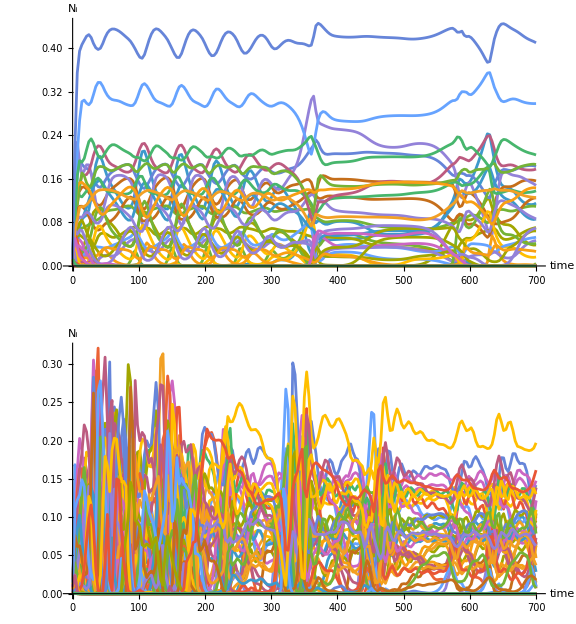

```mathematica
ρtest = 0.4;
μtest = 50.0;
σtest = 5.0;

paramTestA = <|"M" -> 150, "S" -> 150, "ρ" -> ρtest, "μc" -> μtest, "σc" -> σtest, "μg" -> μtest, "σg" -> σtest,
			  "μd" -> 0.0, "σd" -> 0.0, "μb" -> 1.0, "σb" -> 0.0, "μo" -> 1.0, "σo" -> 0.0|>;
			  
paramTestB = <|"M" -> 150, "S" -> 150, "ρ" -> ρtest, "μc" -> μtest, "σc" -> σtest, "μg" -> μtest, "σg" -> σtest,
			  "μd" -> 0.0, "σd" -> 0.0, "μb" -> 1.0, "σb" -> 0.0|>;

simulationTestA = AbioticELV[paramTestA, <|"tEnd" -> 700|>];
simulationTestB = BioticELV[paramTestB, <|"tEnd" -> 700|>];

NdynamicsA = Table[simulationTestA["ConsumerDynamics"][[All, alpha]], {alpha, 1, Length[simulationTestA["ConsumerDynamics"][[1, All]]]}];
NdynamicsB = Table[simulationTestB["ConsumerDynamics"][[All, alpha]], {alpha, 1, Length[simulationTestB["ConsumerDynamics"][[1, All]]]}];

Show[GraphicsGrid[{{ListLinePlot[NdynamicsA, AxesLabel->{"time", "N_i"}, DataRange->{0, simulationTestA["EndTime"]}, AspectRatio->0.5, PlotRange -> All]},
				  {ListLinePlot[NdynamicsB, AxesLabel->{"time", "N_i"}, DataRange->{0, simulationTestB["EndTime"]}, AspectRatio->0.5, PlotRange -> All]}}], 
	ImageSize->Large]
```

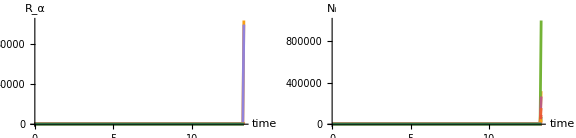

```mathematica
ρtest = 0.4;
μtest = 50.0;
σtest = 10.5;
migrationtest = 10^-4.5;

paramTest = <|"M" -> 150, "S" -> 150, "ρ" -> ρtest, "μc" -> μtest, "σc" -> σtest, "μg" -> μtest, "σg" -> σtest,
			  "μd" -> 1.0, "σd" -> 0.1, "μb" -> migrationtest, "σb" -> 0.0, "μo" -> migrationtest, "σo" -> 0.0|>;

simulationTest = AbioticCRM[paramTest, <|"tEnd" -> 700|>];

Rdynamics = Table[simulationTest["ResourceDynamics"][[ All, alpha]], {alpha, 1, Length[simulationTest["ResourceDynamics"][[1, All]]]}];
Ndynamics = Table[simulationTest["ConsumerDynamics"][[All, alpha]], {alpha, 1, Length[simulationTest["ConsumerDynamics"][[1, All]]]}];

Show[GraphicsGrid[{{ListLinePlot[Rdynamics, AxesLabel->{"time", "R_α"}, DataRange->{0, simulationTest["EndTime"]}, AspectRatio->0.5, PlotRange -> All], 
				  ListLinePlot[Ndynamics, AxesLabel->{"time", "N_i"}, DataRange->{0, simulationTest["EndTime"]}, AspectRatio->0.5, PlotRange -> All]}}], 
	ImageSize->Large]
```